```mathematica
process[raw_]:={#[[2]],#[[1]]}&/@Partition[Select[ToExpression[ToString[Import[raw,"Table"][[1]]]],#≠0&],2];
rawdata=Import["desktop/123.txt","Table"];
rawdata=rawdata[[1]];
data=ToExpression[ToString[rawdata]];
data=Select[data,#≠0&];
data=Partition[data,2];
data={#[[2]],#[[1]]}&/@data;
```

{{-16.5192,28.7663},{-16.5191,28.7665},{-16.519,28.7667},{-16.5189,28.7668},3200,{-15.6232,30.4212},{-15.6228,30.4215},{-15.6225,30.4218}}
 |  |  |  |

```mathematica
GeoGraphics[GeoPath[{{-16.18,23.27},{-17.52,24.29}}],Frame->True]
```

```mathematica
process[raw_]:={#[[2]],#[[1]]}&/@Partition[Select[ToExpression[ToString[Import[raw,"Table"][[1]]]],#≠0&],2];
target="desktop/mcm/123.txt"
data=process[target]
GeoGraphics[{Red,GeoPath[data]},Frame->True]
```

desktop/mcm/123.txt

{{-16.5192,28.7663},{-16.5191,28.7665},{-16.519,28.7667},3202,{-15.6228,30.4215},{-15.6225,30.4218}}
 |  |  |  |

-Graphics-

{{-16.5192,28.7663},{-16.5191,28.7665},{-16.519,28.7667},{-16.5189,28.7668},3200,{-15.6232,30.4212},{-15.6228,30.4215},{-15.6225,30.4218}}
 |  |  |  |

StructuredArray[QuantityArray, {3207}, <Meters>]

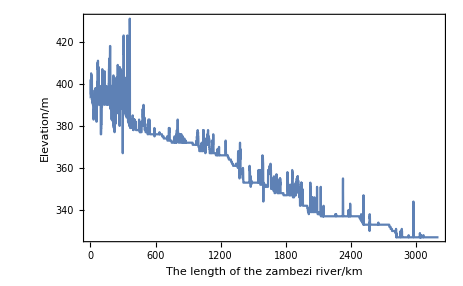

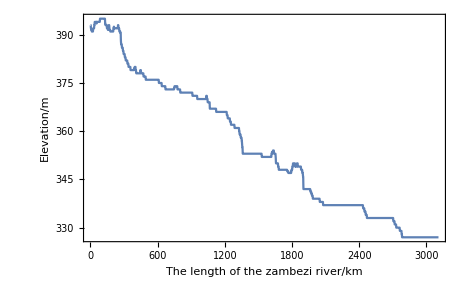

```mathematica
dataEle=GeoElevationData[GeoPosition[data]]
ListPlot[dataEle,Joined->True,Frame->True,FrameLabel->{"The length of the zambezi river/km","Elevation/m"}]
ListPlot[MovingMedian[Normal[dataEle],100],Joined->True,Frame->True,FrameLabel->{"The length of the zambezi river/km","Elevation/m"}]
```

```mathematica
data1=Import["desktop/pos.txt","Table"];
dataWid=data1[[;;,1]];
dataLen=data1[[;;,2]];
movWid=MovingAverage[dataWid,2]//N
Export["desktop/movWid.xlsx",movWid]
```

{335.,353.,647.,1184.5,1109.5,931.5,953.,546.5,361.5,369.5,358.,529.5,566.5,588.,740.,882.,887.5,626.5,604.,690.,710.,670.5,490.5,1421.,1551.5,546.5,542.5,499.,503.,844.5,719.,470.5,766.5,689.5,597.5,876.,654.5,644.,927.5,934.,1020.5,1158.5,1173.5,1147.,802.,430.,492.5,895.5,1019.5}

desktop/movWid.xlsx

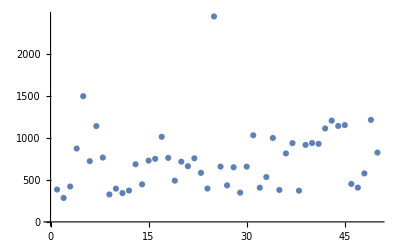

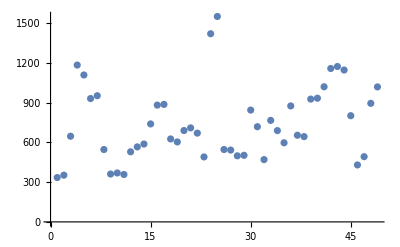

```mathematica
ListPlot[dataWid]
ListPlot[movWid]
```

```mathematica
process[raw_]:={#[[2]],#[[1]]}&/@Partition[Select[ToExpression[ToString[Import[raw,"Table"][[1]]]],#≠0&],2];
target="desktop/upper.txt"
data=process[target];
GeoGraphics[{Red,GeoPath[data]},Frame->True]
dataEle=GeoElevationData[GeoPosition[data]]
ListPlot[dataEle,Joined->True,Frame->True,FrameLabel->{"The length of the zambezi river/km","Elevation/m"}]
ListPlot[MovingMedian[Normal[dataEle],100],Joined->True,Frame->True,FrameLabel->{"The length of the zambezi river/km","Elevation/m"}]
```

desktop/upper.txt

-Graphics-

```mathematica
process[raw_]:={#[[2]],#[[1]]}&/@Partition[Select[ToExpression[ToString[Import[raw,"Table"][[1]]]],#≠0&],2];target1="desktop/mcm/123.txt";
data1=process[target1];
target2="desktop/upper.txt";
data2=process[target2];
target3="desktop/ex.txt";
data3=process[target3];
data3=Drop[data3,9]
GeoGraphics[{Red,GeoPath[data1],Red,GeoPath[data2[[5400;;]]],GeoMarker[data3,Scale->0.08]},Frame->True]
```

{{-17.9543,25.86},{-17.9819,25.8994},{-18.0002,25.9639},{-17.9729,26.045},{-17.9808,26.0624},{-17.9812,26.0921},{-17.9337,26.095},{-17.9044,26.1815},{-17.918,26.2455},{-17.9307,26.3551},{-17.9652,26.4579},{-18.0184,26.5768},{-18.0752,26.6846},{-18.0089,26.8307},{-17.9842,26.878},{-16.2581,28.8532},{-16.0978,28.866},{-16.0395,28.8529},{-15.9431,28.9815},{-15.9164,29.038},{-15.8735,29.0928},{-15.8398,29.1314},{-15.7706,29.2175},{-15.7165,29.3642},{-15.6826,29.5117},{-15.6586,29.5959},{-15.6374,29.7351},{-15.6313,29.9476},{-15.6434,30.2738},{-15.6543,30.3605}}

-Graphics-

```mathematica
sell={1,2,4,5,6,8,9,10,11,12,13,18,20,27,28,29}
seleSite=data3[[sell]]
GeoGraphics[{Red,GeoPath[data1],Red,GeoPath[data2[[5400;;]]],GeoMarker[seleSite,Scale->0.12]},Frame->True]
```

{1,2,4,5,6,8,9,10,11,12,13,18,20,27,28,29}

{{-17.9543,25.86},{-17.9819,25.8994},{-17.9729,26.045},{-17.9808,26.0624},{-17.9812,26.0921},{-17.9044,26.1815},{-17.918,26.2455},{-17.9307,26.3551},{-17.9652,26.4579},{-18.0184,26.5768},{-18.0752,26.6846},{-16.0395,28.8529},{-15.9164,29.038},{-15.6374,29.7351},{-15.6313,29.9476},{-15.6434,30.2738}}

-Graphics-

```mathematica
sell={1,2,4,5,6,8,9,10,11,12,13,18,20,27,28,29}
seleSite=data3[[sell]]
GeoGraphics[{Red,GeoPath[data1],Red,GeoPath[data2[[5400;;]]],GeoMarker[seleSite,Scale->0.12]},Frame->True]
```

{1,2,4,5,6,8,9,10,11,12,13,18,20,27,28,29}

{{-17.9543,25.86},{-17.9819,25.8994},{-17.9729,26.045},{-17.9808,26.0624},{-17.9812,26.0921},{-17.9044,26.1815},{-17.918,26.2455},{-17.9307,26.3551},{-17.9652,26.4579},{-18.0184,26.5768},{-18.0752,26.6846},{-16.0395,28.8529},{-15.9164,29.038},{-15.6374,29.7351},{-15.6313,29.9476},{-15.6434,30.2738}}

```mathematica
MatrixForm[seleSite]
```

(-17.9543 | 25.86
-17.9819 | 25.8994
-17.9729 | 26.045
-17.9808 | 26.0624
-17.9812 | 26.0921
-17.9044 | 26.1815
-17.918 | 26.2455
-17.9307 | 26.3551
-17.9652 | 26.4579
-18.0184 | 26.5768
-18.0752 | 26.6846
-16.0395 | 28.8529
-15.9164 | 29.038
-15.6374 | 29.7351
-15.6313 | 29.9476
-15.6434 | 30.2738)

```mathematica
TableForm[seleSite]
```

-17.9543 | 25.86
-17.9819 | 25.8994
-17.9729 | 26.045
-17.9808 | 26.0624
-17.9812 | 26.0921
-17.9044 | 26.1815
-17.918 | 26.2455
-17.9307 | 26.3551
-17.9652 | 26.4579
-18.0184 | 26.5768
-18.0752 | 26.6846
-16.0395 | 28.8529
-15.9164 | 29.038
-15.6374 | 29.7351
-15.6313 | 29.9476
-15.6434 | 30.2738

```mathematica
data3=Drop[data3,1]
```

{{-17.8477,25.3883},{-17.8571,25.4946},{-17.8466,25.5401},{-17.841,25.6048},{-17.8269,25.6993},{-17.8404,25.7199},{-17.8781,25.7959},{-17.8972,25.8439},{-17.9543,25.86},{-17.9819,25.8994},{-18.0002,25.9639},{-17.9729,26.045},{-17.9808,26.0624},{-17.9812,26.0921},{-17.9337,26.095},{-17.9044,26.1815},{-17.918,26.2455},{-17.9307,26.3551},{-17.9652,26.4579},{-18.0184,26.5768},{-18.0752,26.6846},{-18.0089,26.8307},{-17.9842,26.878},{-16.2581,28.8532},{-16.0978,28.866},{-16.0395,28.8529},{-15.9431,28.9815},{-15.9164,29.038},{-15.8735,29.0928},{-15.8398,29.1314},{-15.7706,29.2175},{-15.7165,29.3642},{-15.6826,29.5117},{-15.6586,29.5959},{-15.6374,29.7351},{-15.6313,29.9476},{-15.6434,30.2738},{-15.6543,30.3605}}

```mathematica
dataEle=GeoElevationData[GeoPosition[data2[[1;;5000]]]]
Geo
```

GeoElevationData::datap: Unable to download elevation data for positions GeoPosition[{{-16.2463,23.242},{-16.2468,23.2423},{-16.2474,23.2426},«45»,{-16.2686,23.2522},{-16.2689,23.2524},«5150»}].

$Aborted

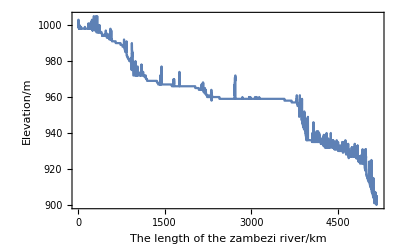

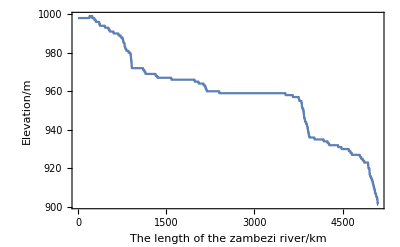

```mathematica
ListPlot[dataEle,Joined->True,Frame->True,FrameLabel->{"The length of the zambezi river/km","Elevation/m"}]
ListPlot[MovingMedian[Normal[dataEle],100],Joined->True,Frame->True,FrameLabel->{"The length of the zambezi river/km","Elevation/m"}]
```

```mathematica
data
```

data

```mathematica
Export["desktop/site_all.csv",data3]
```

desktop/site_all.csv

```mathematica
TableForm[%64]
```

-17.8571 | 25.4946
-17.9543 | 25.86
-17.9819 | 25.8994
-17.9808 | 26.0624
-17.918 | 26.2455
-17.9652 | 26.4579
-18.0752 | 26.6846
-16.0978 | 28.866
-15.9431 | 28.9815
-15.6313 | 29.9476

```mathematica
da
```

```mathematica
Dimensions@data3
```

{38,2}

```mathematica
target3="desktop/ex.txt";
data3=process[target3];
Dimensions@data3
```

{39,2}

```mathematica
temp={};
Do[AppendTo[temp,GeoDistance[data1[[(n);;(n+1)]]]],{n,Length[data1]-1}];
dis=Accumulate[temp];
```

$Aborted

```mathematica
temp=QuantityMagnitude@temp;
dis=Accumulate[temp];
PrependTo[dis,0];
distances=QuantityArray[dis,"Meters"]
dataEle=ElevationData[GeoPosition[data1]];ListPlot[Transpose[{distances,data1}],Joined->True]
```

```mathematica
ElevationData
```

ElevationData[GeoPosition[…]]

```mathematica
Join
```

```mathematica
GeoDi
```

{23.2478 m,19.2309 m,22.9059 m,24.3867 m,20.4517 m,12.8286 m,11.9839 m,18.1425 m,21.7022 m,24.0221 m}

```mathematica
Dimensions[data3]
```

{30,2}